# Attempting time-dependent dynamics using glacier retreat to drive landsliding

## First define functions that provide topography as a function of material parameters and geometry

```mathematica
(*First define Modules for Ice and No-ice cases*)
ComputeIceProfile[
x0_?NumericQ,k_?NumericQ,bmax_?NumericQ,αv_?NumericQ,fv_?NumericQ,ρ_?NumericQ]:=Module[{θv,HBC,hg,solice,Hsol,Hice,hice,sollogss,h,bviNum,DbviNum,Dbvi2Num,xendice},
(*Fixed parameters*)
θv=ArcTan[αv];
xendice = 1.0;
(*Basal topography and its derivatives as numeric functions*)
bviNum[x_]:=bmax*((x-x0)^2-1);
DbviNum[x_]:=2 bmax (x-x0);
Dbvi2Num[x_]:=2 bmax;
(*H=h-b boundary condition*)
HBC=k*Abs[bviNum[0]];
hg=k*HBC+bviNum[0];
(*Solve ice-covered ODE*)solice=NDSolve[{(ρ-1) (H'[x]+DbviNum[x])-0.5*((Tan[θv]-DbviNum[x])/(1+DbviNum[x]^2)*Dbvi2Num[x]/(1+DbviNum[x] Tan[θv]))*H[x]-ρ*(hg-H[x]-bviNum[x]+x Tan[θv])*(fv/H[x]+Dbvi2Num[x]*(Tan[θv]/(1+DbviNum[x] Tan[θv])-DbviNum[x]/(1+DbviNum[x]^2)))==fv+ρ Tan[θv]-(Tan[θv]-DbviNum[x])/(1+DbviNum[x] Tan[θv]),
H[0]==HBC,
WhenEvent[H[x]<=10^-7,{xendice=x,"StopIntegration"}]},
H,{x,0,1+x0}];
Hsol[x_]:=(H[x]/. solice[[1]]);
Hice[x_]:=If[0<=x<=xendice,Hsol[x],0];
hice[x_]:=bviNum[x]+Hice[x];
hice]

ComputeDryProfile[
x0_?NumericQ,k_?NumericQ,bmax_?NumericQ,αv_?NumericQ,fv_?NumericQ]:=Module[{θv,bviNum,DbviNum,Dbvi2Num,HBC,hg,eqnlogODE,sollogss,phiFun,hdry},
(*fixed*)
θv=ArcTan[αv];
(*basal topography and derivatives (explicit numeric functions)*)
bviNum[x_]:=bmax*((x-x0)^2-1);
DbviNum[x_]:=2 bmax (x-x0);
Dbvi2Num[x_]:=2 bmax;
(*boundary condition*)
HBC=k*Abs[bviNum[0]];
hg=k*HBC+bviNum[0];
(*ODE for phi (log H) for ice-free region*)eqnlogODE=-Exp[phi[x]]*phi'[x]-0.5*(Tan[θv]-DbviNum[x])/(1+DbviNum[x]^2)*Dbvi2Num[x]/(1+DbviNum[x]*Tan[θv])*Exp[phi[x]]==fv+DbviNum[x]-(Tan[θv]-DbviNum[x])/(1+DbviNum[x]*Tan[θv]);
(*Solve on an x-interval that covers the dry region.
Adjust left endpoint if you want a different domain.*)sollogss=NDSolve[{eqnlogODE,phi[0]==Log[HBC],WhenEvent[phi[x]<=-6,"StopIntegration"]},phi,{x,-1+x0,0}];
(*make phi an explicit function of x*)
phiFun[x_]:=(phi[x]/. sollogss[[1]]);
(*the dry profile h=b+H with H=Exp[phi]*)
hdry[x_]:=bviNum[x]+Exp[phiFun[x]];
hdry]

ComputeLandslideVolume[
x0_?NumericQ,k_?NumericQ,b0_?NumericQ,α_?NumericQ,f_?NumericQ,ρ_?NumericQ]:=Module[{hice,hdry,h,Harea},
(*get ice and dry profiles*)
hice=ComputeIceProfile[x0,k,b0,α,f,ρ];
hdry=ComputeDryProfile[x0,k,b0,α,f];
(*combined profile*)
h[x_]:=Piecewise[{{hdry[x],-1+x0<=x<=0},{hice[x],0<x<=1+x0}},0];
(*integrate volume (area under h-base)*)
Harea=NIntegrate[h[x]-b[x,b0,x0],{x,-1+x0,1+x0}];
Harea]

FindOptimalK[
x0_?NumericQ,b0_?NumericQ,α_?NumericQ,f_?NumericQ,ρ_?NumericQ,Volume_?NumericQ]:=(*Module[{results,misfit,minIndex},*)(*results=ParallelTable[{k,ComputeLandslideVolume[x0,k,b0,α,f,ρ]},{k,0.05,1.5,0.025}];
misfit=Abs[(results[[All,2]]-Volume)];
minIndex=First@Ordering[misfit,1];
results[[minIndex,1]] (*return the k value only*)*)

Module[{misfit,sol},
(*define misfit function:squared error in volume*)misfit[k_?NumericQ]:=(ComputeLandslideVolume[x0,k,b0,α,f,ρ]-Volume)^2;
(*minimize misfit over reasonable domain*)
sol=FindMinimum[{misfit[k],0.01<=k<=2},{k,1.0},AccuracyGoal->1,PrecisionGoal->1];
k/. Last[sol]  (*extract optimal k*)
]
```

## Compute profiles for initial and final state

InterpolatingFunction::dmval: Input value {-0.999959} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::munfl: Exp[-935020.] is too small to represent as a normalized machine number; precision may be lost.

InterpolatingFunction::dmval: Input value {-0.999959} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::munfl: Exp[-964262.] is too small to represent as a normalized machine number; precision may be lost.

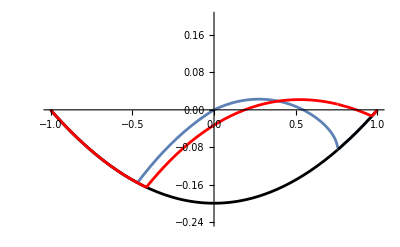

```mathematica
(*Specify parameters*)
α = 0.4;
θ = ArcTan[α];
f = 0.17;
ρ = 0.2;(*ratio of ice/rock density*)
k = 1.0;
b0 = 0.2;
x0 = -0.0;
(* quadratic basal topography*)
b[x_,b0_,x0_] := b0*((x-x0)^2-1);

(*Compute landslide profile*)
hice=ComputeIceProfile[x0,k,b0,α,f,ρ];
hdry = ComputeDryProfile[x0,k,b0,α,f];
(*Combine hdry and hice*)
h[x_]:=Piecewise[{{hdry[x],-1+x0<=x<=0},{hice[x],0<x<=1+x0}},0]
(*Compute Volume of landslide*)
VolOriginal=ComputeLandslideVolume[x0,k,b0,α,f,ρ];

(*Compute dry profile*)
kDry=FindOptimalK[0,b0,α,f,ρ*0,VolOriginal];
(*Compute landslide profile*)
haR=ComputeIceProfile[0,kDry,b0,α,f,ρ*0];
haL = ComputeDryProfile[0,kDry,b0,α,f];
(*Combine for dry profile*)
hafter[x_]:=Piecewise[{{haL[x],-1<=x<=0},{haR[x],0<x<=1}},0]

(*Plot landslide profile*)
Plot[{h[x],b[x,b0,x0],hafter[x]},{x,-1+x0,1+x0},PlotStyle->{DarkBlue,Black,Red},PlotRange->{-1.2*b0,b0}]
```

## Optimize ‘k’ as ice level moves to x>0

```mathematica
kTable=Table[
{x0val,FindOptimalK[x0val,b0,α,f,ρ,VolOriginal]},{
x0val,0,-0.9,-0.1}   (*step backwards in x0*)]
x0vals =kTable[[All,1]];
kvals=kTable[[All,2]];
```

{{0.,1.},{-0.1,1.07734},{-0.2,1.13312},{-0.3,1.17248},{-0.4,1.19843},{-0.5,1.21205},{-0.6,1.21195},{-0.7,1.19162},{-0.8,1.12857},{-0.9,0.912189}}

## Now evaluate height time series at a select point

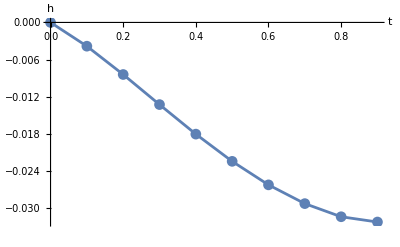

```mathematica
xObsPoint = 0.0;
hdryTable=
Table[Module[{hdry},hdry=ComputeDryProfile[x0vals[[i]],kvals[[i]],b0,α,f];
{x0vals[[i]],hdry[xObsPoint+x0vals[[i]]]}],{i,Length[x0vals]}];
ListLinePlot[Transpose[{-hdryTable[[All,1]],hdryTable[[All,2]]}],AxesLabel->{Style["t",15],Style["h",15]},PlotMarkers->Automatic,PlotStyle->DarkBlue,PlotRange->Full]
```

InterpolatingFunction::dmval: Input value {-1.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::munfl: Exp[-935226.] is too small to represent as a normalized machine number; precision may be lost.

InterpolatingFunction::dmval: Input value {-0.99} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::munfl: Exp[-883975.] is too small to represent as a normalized machine number; precision may be lost.

InterpolatingFunction::dmval: Input value {-0.98} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

General::munfl: Exp[-834631.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {-0.999959} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::munfl: Exp[-964262.] is too small to represent as a normalized machine number; precision may be lost.

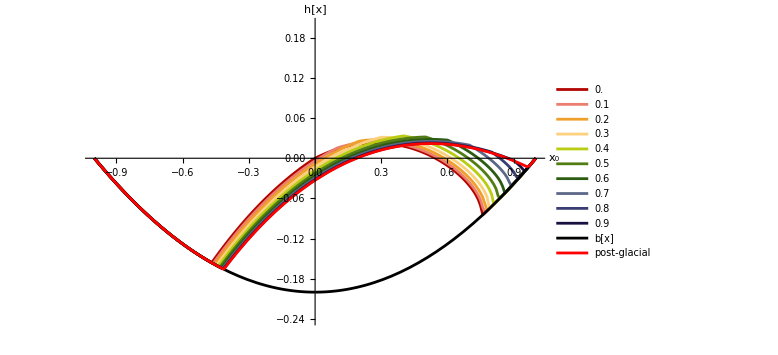

```mathematica
hProfiles=Table[
Module[{x0,k,hdry,hice,hFunc,xVals},
{x0,k}=kTable[[i]];
(*Compute dry and ice profiles*)
hdry=ComputeDryProfile[x0,k,b0,α,f];
hice=ComputeIceProfile[x0,k,b0,α,f,ρ];
(*Define combined h[x]*)hFunc[x_]:=Piecewise[{{hdry[x],-1+x0<=x<=0},{hice[x],0<x<=1+x0}},0];
(*x-values specific to this profile*)
xVals=Range[-1+x0,1+x0,0.01];
{xVals-x0,hFunc/@xVals}  (*store x and h[x]*)
],
{i,Length[kTable]}
];

p1=ListLinePlot[
Table[
Transpose[hProfiles[[i]]],(*{{x1,h1},{x2,h2},...}*)
{i,Length[hProfiles]}
],
PlotStyle->Table[ColorData[10][i],{i,Length[hProfiles]}],
AxesLabel->{Subscript[x,0],"h[x]"},PlotLegends->Placed[Table[ToString[Abs[kTable[[i,1]]]],{i,Length[kTable]}],Right],ImageSize->Large];
p2 = Plot[{b[x,b0,x0],hafter[x]},{x,-1,1},PlotStyle->{Black,Red},PlotLegends->{"b[x]","post-glacial"}];
Show[p1,p2,PlotRange->{-b0*1.2,b0}]
```